C:\Users\DANIEL\Desktop\SIMPL

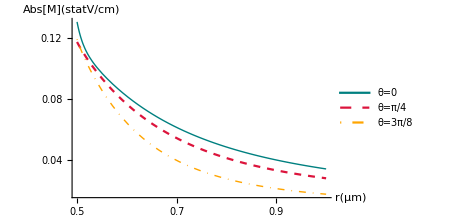

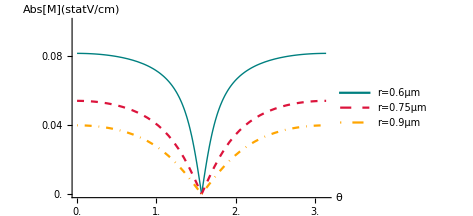

magnetization_r.png

magnetization_theta.png

```mathematica
α=1/137;
ϵ=4; (*permitividad relativa*)
c=10^(-4); (*factor para pasar de micras a cm 1micra=10^(-4)cm*)
s=c; (*este es r2, que es 1micra=10^(-4)cm*)
a=0.5*c; (*puede ser 0.5, 0.62 y 0.75*) (*order of approximation*)
n=20;
SetDirectory[NotebookDirectory[]]
ticksv[min_,max_]:=Table[{i,Style[i,10],{0.02,0},Directive[Black]},{i,0.000,max,0.02}]

ticksh[min_,max_]:=Table[{i,Style[i,10],{0.02,0},Directive[Black]},{i,0.5,max,0.1}]
ticksh2[min_,max_]:=Table[{i,Style[i,10],{0.02,0},Directive[Black]},{i,0,max,0.5}]

V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
(*esta es la funcion Vl*)
A[l_]:=(l+1)*(ϵ-1)*(a^(l+1)*V[l]/(a^(2l+1)*(ϵ-1)(l+1)+(l*ϵ+l+1)*s^(2l+1)));
(*coeficiente A_l^2*) 
B[l_]:=s^(2l+1)*(l*ϵ+l+1)*(a^(l+1)*V[l]/(a^(2l+1)*(ϵ-1)(l+1)+(l*ϵ+l+1)*s^(2l+1)))
(*coeficiente B_l^2*) 

Φr[r_]:=Sum[(A[2l+1]*r^(2l+1)+B[2l+1]*r^(-2(l+1)))*LegendreP[2l+1,Cos[θ]],{l,0,n}];
Φθ[θ_]:=Sum[(A[2l+1]*r^(2l+1)+B[2l+1]*r^(-2(l+1)))*LegendreP[2l+1,Cos[θ]],{l,0,n}];
E2[r_,θ_]=Sqrt[(D[Φr[r]])^2+(1/r*D[Φθ[θ]])^2];
M2[r_,θ_]:=α/(4*Pi)*E2[r,θ];
plt1=Show[Plot[M2[c*r,0],{r,0.5,1},PlotLegends->Placed[{"θ=0"},{0.8,0.9}],PlotRange->All,PlotStyle->{RGBColor[0,128/255,128/255],Thick}],
Plot[M2[c*r,Pi/4],{r,0.5,1},PlotLegends->Placed[{"θ=π/4"},{0.8,0.8}],PlotRange->All,PlotStyle->{RGBColor[220/255,20/255,60/255],Dashed}],
Plot[M2[c*r,3*Pi/8],{r,0.5,1},PlotLegends->Placed[{"θ=3π/8"},{0.8,0.7}],PlotRange->All,PlotStyle->{RGBColor[1,165/255,0],Thick,DotDashed}], AxesOrigin->{Automatic,0},PlotRange->All,AxesLabel->{Style["r(μm)",12],Style[Abs[M]["statV/cm"],12]},AxesStyle->Black,ImageSize->350,Ticks->{ticksh,ticksv}]
plt2=Show[Plot[M2[c*0.6,θ],{θ,0,Pi},PlotLegends->Placed[{"r=0.6μm"},{0.5,0.94}],PlotRange->All,PlotStyle->{RGBColor[0,128/255,128/255],Thick}],
Plot[M2[c*0.75,θ],{θ,0,Pi},PlotLegends->Placed[{"r=0.75μm"},{0.5,0.84}],PlotRange->All,PlotStyle->{RGBColor[220/255,20/255,60/255],Dashed}],
Plot[M2[c*0.9,θ],{θ,0,Pi},PlotLegends->Placed[{"r=0.9μm"},{0.5,0.74}],PlotRange->All,PlotStyle->{RGBColor[1,165/255,0],DotDashed}], AxesOrigin->{Automatic,0},PlotRange->{0,0.1},AxesLabel->{Style["θ",12],Style[Abs[M]["statV/cm"],12]},AxesStyle->Black,ImageSize->350,Ticks->{ticksh2,ticksv}]
Export["magnetization_r.png",plt1,ImageResolution->600]
Export["magnetization_theta.png",plt2,ImageResolution->600]
```